# Lab 5 - Grapefruit

```mathematica
Needs["PlotLegends`"]
dir = NotebookDirectory[];
SetDirectory[dir];
```

Let the full v0 be fixed to start arbitrarily at 10

```mathematica
v0test = 10;
```

```mathematica
d[x0_,v0_,t_, th_] := x0 + v0* Cos[th] * t
```

Flight distance in the abscence of drag is only dependent on the x component of the velocity, which is v0 times the cosine of the firing angle.

```mathematica
thetas = Table[th, {th, 0, Pi/2, Pi/36}]
```

{0,π/36,π/18,π/12,π/9,(5 π)/36,π/6,(7 π)/36,(2 π)/9,π/4,(5 π)/18,(11 π)/36,π/3,(13 π)/36,(7 π)/18,(5 π)/12,(4 π)/9,(17 π)/36,π/2}

```mathematica
data =Map[Function[th,d[0,10,x,th]], thetas]
```

{10 x,10 x Cos[π/36],10 x Cos[π/18],(5 (1+√3) x)/(√2),10 x Cos[π/9],10 x Cos[(5 π)/36],5 √3 x,10 x Cos[(7 π)/36],10 x Cos[(2 π)/9],5 √2 x,10 x Sin[(2 π)/9],10 x Sin[(7 π)/36],5 x,10 x Sin[(5 π)/36],10 x Sin[π/9],(5 (-1+√3) x)/(√2),10 x Sin[π/18],10 x Sin[π/36],0}

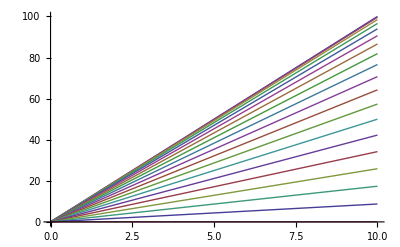

```mathematica
Plot[data, {x, 0, 10}]
```